```mathematica
N[Pi,100];
N[E,10];
Sum[1/k^2,{k,1,Infinity}];
NSum[1/k^2,{k,1,Infinity}];
Product[n^3,{n,1,5}];
Product[k^2,{k,2,8,2}];
Integrate[y,y];
Integrate[1/(1+y^2),y];
Integrate[1/(1+y^2),{y,0,1}];
Limit[(1+1/n)^n,n->Infinity];
Solve[{z+y==5,3z-2y==7},{z,y}];
Expand[(z-y)*(z+y)];
Factor[%];
Series[yCot[y],{y,0,8}];
```

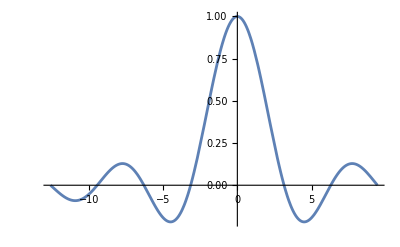

```mathematica
f[x_]:=Sin[x]/x;
Plot[f[x],{x,-4Pi,3Pi},PlotRange->All]
```

```mathematica
g[x_,y_]:=Sin[x*y]+Cos[x^2+y^2];
Plot3D[g[x,y],{x,0,2Pi},{y,0,2Pi},Mesh->False]
```

-Graphics3D-

```mathematica
If[2==3,5,6]
```

6

```mathematica
y=0
Do[y=y+k,{k,1,99,2}]
y
```

0

2500

```mathematica
y=0
x=2
While[x<101,y=y+x;x=x+2]
y
```

0

2

2550

Solve::ivar: 5 is not a valid variable.